```mathematica
ClearAll["Global`*"]
```

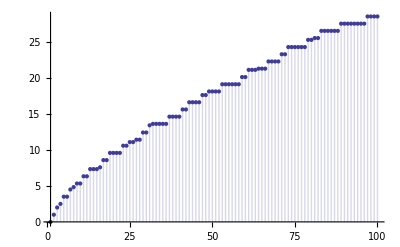

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
DD[n_,z_]:=DD[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1b[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1b[n/b^j,k,b],{j,0,Log[b,n]}]
E1b[n_,k_,b_]:=Sum[FactorialPower[k,a]/a! E2b[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
E2b[n_,k_, a_]:= E2b[n,k,a]=Sum[ E2b[n/j,k-1,a],{j,2,n}]+a Sum[ E2b[n/(a j),k-1,a],{j,1,n/a}];E2b[n_,0,a_]:=1
D1c[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (-1)^j
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D1d[n_, z_, b_] := Sum[ 
Binomial[z+j-1,z-1]  Binomial[z,k]b^j (-1)^j  E2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]
D1e[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  Binomial[k,a]b^j (-1)^j  E2[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1e2[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  FactorialPower[k,a]/a!b^j (-1)^j  E2[n/b^j,a,b]/k,{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1c2[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j (-1)^j
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
lin[n_,b_]:=Sum[(-1)^(k+1)/k E2b[n,k,b],{k,1,Log[b,n]}]
M2[n_,a_]:=Sum[(-1)^k( E2b[n,k,a]-a E2b[n/a,k,a]),{k,0,Log[a,n]}]

DiscretePlot[ (DD[n,.000001]-1)/.000001,{n,1,100}]

DiscretePlot[ (DD[n,.000001]-1)/.000001-lin[n,2],{n,1,100}]
```

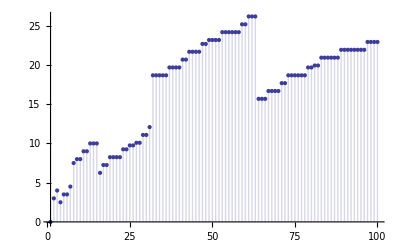

```mathematica
DiscretePlot[ lin[n,2],{n,1,100}]
```

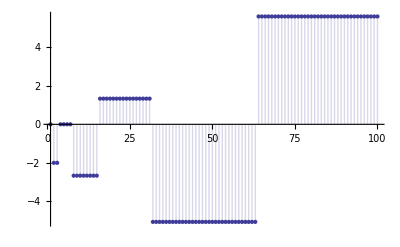

```mathematica
DiscretePlot[ (DD[n,.000001]-1)/.000001-lin[n,2],{n,1,100}]
```

```mathematica
fdif[n_, a_] := Sum[ (-1)^k a^k / k, {k,1,Log[a,n]}]
fdif[100,1.000001]
```

-0.693147+0.0000108508 ⅈ

```mathematica
Limit[Sum[ (-1)^k a^k / k, {k,1,Log[a,n]}],a->1]
```

Limit[(-1)^(Log[n]/Log[a]) a n LerchPhi[-a,1,1+Log[n]/Log[a]]-Log[1+a],a→1]

```mathematica
D1c[30,-1,1.1]
```

-3.

```mathematica
(D1c2[100,.0000001,2]-1)/.0000001
```

28.5333

```mathematica
lin[100,2]
```

344/15

```mathematica
D1e2[100,.0000001,2]
```

1.×10^7 E2[100,0,2] | 1. E2[100,1,2] | -0.5 E2[100,2,2] | 0.333333 E2[100,3,2] | -0.25 E2[100,4,2] | 0.2 E2[100,5,2] | -0.166667 E2[100,6,2]
-2. E2[50,0,2] | -2.×10^-7 E2[50,1,2] | 1.×10^-7 E2[50,2,2] | -6.66667×10^-8 E2[50,3,2] | 5.×10^-8 E2[50,4,2] | -4.×10^-8 E2[50,5,2] | 
2. E2[25,0,2] | 2.×10^-7 E2[25,1,2] | -1.×10^-7 E2[25,2,2] | 6.66667×10^-8 E2[25,3,2] | -5.×10^-8 E2[25,4,2] |  | 
-2.66667 E2[25/2,0,2] | -2.66667×10^-7 E2[25/2,1,2] | 1.33333×10^-7 E2[25/2,2,2] | -8.88889×10^-8 E2[25/2,3,2] |  |  | 
4. E2[25/4,0,2] | 4.×10^-7 E2[25/4,1,2] | -2.×10^-7 E2[25/4,2,2] |  |  |  | 
-6.4 E2[25/8,0,2] | -6.4×10^-7 E2[25/8,1,2] |  |  |  |  | 
10.6667 E2[25/16,0,2] |  |  |  |  |  |

```mathematica
D1e[100,-1,2]
```

E2[100,0,2] | -E2[100,1,2] | E2[100,2,2] | -E2[100,3,2] | E2[100,4,2] | -E2[100,5,2] | E2[100,6,2]
2 E2[50,0,2] | -2 E2[50,1,2] | 2 E2[50,2,2] | -2 E2[50,3,2] | 2 E2[50,4,2] | -2 E2[50,5,2] | 
0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
D1e[900,1,2]
```

E2[900,0,2] | E2[900,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 E2[450,0,2] | -2 E2[450,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
4 E2[225,0,2] | 4 E2[225,1,2] | 0 | 0 | 0 | 0 | 0 | 0 |  | 
-8 E2[225/2,0,2] | -8 E2[225/2,1,2] | 0 | 0 | 0 | 0 | 0 |  |  | 
16 E2[225/4,0,2] | 16 E2[225/4,1,2] | 0 | 0 | 0 | 0 |  |  |  | 
-32 E2[225/8,0,2] | -32 E2[225/8,1,2] | 0 | 0 | 0 |  |  |  |  | 
64 E2[225/16,0,2] | 64 E2[225/16,1,2] | 0 | 0 |  |  |  |  |  | 
-128 E2[225/32,0,2] | -128 E2[225/32,1,2] | 0 |  |  |  |  |  |  | 
256 E2[225/64,0,2] | 256 E2[225/64,1,2] |  |  |  |  |  |  |  | 
-512 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,2,2]
```

E2[900,0,2] | 2 E2[900,1,2] | E2[900,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4 E2[450,0,2] | -8 E2[450,1,2] | -4 E2[450,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 
12 E2[225,0,2] | 24 E2[225,1,2] | 12 E2[225,2,2] | 0 | 0 | 0 | 0 | 0 |  | 
-32 E2[225/2,0,2] | -64 E2[225/2,1,2] | -32 E2[225/2,2,2] | 0 | 0 | 0 | 0 |  |  | 
80 E2[225/4,0,2] | 160 E2[225/4,1,2] | 80 E2[225/4,2,2] | 0 | 0 | 0 |  |  |  | 
-192 E2[225/8,0,2] | -384 E2[225/8,1,2] | -192 E2[225/8,2,2] | 0 | 0 |  |  |  |  | 
448 E2[225/16,0,2] | 896 E2[225/16,1,2] | 448 E2[225/16,2,2] | 0 |  |  |  |  |  | 
-1024 E2[225/32,0,2] | -2048 E2[225/32,1,2] | -1024 E2[225/32,2,2] |  |  |  |  |  |  | 
2304 E2[225/64,0,2] | 4608 E2[225/64,1,2] |  |  |  |  |  |  |  | 
-5120 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
DD[100,-1]
```

1

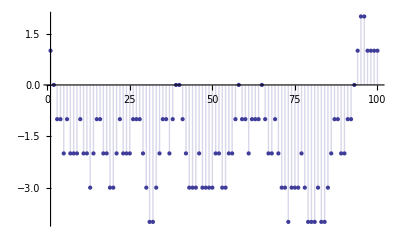

```mathematica
DiscretePlot[ DD[n,-1],{n,1,100}]
```

```mathematica
DiscretePlot[ EE[n,-1,200],{n,1,100}]
```

-Graphics-

```mathematica
Animate[DiscretePlot[ EE[n,7,z],{n,1,100}],{z,2,100}]
```

```mathematica
Animate[DiscretePlot[ EE[n,-1,z],{n,1,100}],{z,2,100}]
```

```mathematica
Animate[DiscretePlot[( EE[n,.0001,z]-1)/.0001,{n,1,100}],{z,2,100}]
```

```mathematica
D1d[1000,-3/2,2]
```

-143/128 E2[125/64,0,2]+99/128 E2[125/32,0,2]-297/256 E2[125/32,1,2]-9/16 E2[125/16,0,2]+27/32 E2[125/16,1,2]-135/128 E2[125/16,2,2]+7/16 E2[125/8,0,2]-21/32 E2[125/8,1,2]+105/128 E2[125/8,2,2]-245/256 E2[125/8,3,2]-3/8 E2[125/4,0,2]+9/16 E2[125/4,1,2]-45/64 E2[125/4,2,2]+105/128 E2[125/4,3,2]-(945 E2[125/4,4,2])/1024+3/8 E2[125/2,0,2]-9/16 E2[125/2,1,2]+45/64 E2[125/2,2,2]-105/128 E2[125/2,3,2]+(945 E2[125/2,4,2])/1024-(2079 E2[125/2,5,2])/2048-1/2 E2[125,0,2]+3/4 E2[125,1,2]-15/16 E2[125,2,2]+35/32 E2[125,3,2]-315/256 E2[125,4,2]+693/512 E2[125,5,2]-(3003 E2[125,6,2])/2048+3/2 E2[250,0,2]-9/4 E2[250,1,2]+45/16 E2[250,2,2]-105/32 E2[250,3,2]+945/256 E2[250,4,2]-2079/512 E2[250,5,2]+(9009 E2[250,6,2])/2048-(19305 E2[250,7,2])/4096+3 E2[500,0,2]-9/2 E2[500,1,2]+45/8 E2[500,2,2]-105/16 E2[500,3,2]+945/128 E2[500,4,2]-2079/256 E2[500,5,2]+(9009 E2[500,6,2])/1024-(19305 E2[500,7,2])/2048+(328185 E2[500,8,2])/32768+E2[1000,0,2]-3/2 E2[1000,1,2]+15/8 E2[1000,2,2]-35/16 E2[1000,3,2]+315/128 E2[1000,4,2]-693/256 E2[1000,5,2]+(3003 E2[1000,6,2])/1024-(6435 E2[1000,7,2])/2048+(109395 E2[1000,8,2])/32768-(230945 E2[1000,9,2])/65536

```mathematica
D1e[900,-1,2]
```

E2[900,0,2] | -E2[900,1,2] | E2[900,2,2] | -E2[900,3,2] | E2[900,4,2] | -E2[900,5,2] | E2[900,6,2] | -E2[900,7,2] | E2[900,8,2] | -E2[900,9,2]
2 E2[450,0,2] | -2 E2[450,1,2] | 2 E2[450,2,2] | -2 E2[450,3,2] | 2 E2[450,4,2] | -2 E2[450,5,2] | 2 E2[450,6,2] | -2 E2[450,7,2] | 2 E2[450,8,2] | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1f[n_, k_, b_] := Sum[ 
Binomial[k+j-1,k-1]  Binomial[k,a]b^j  E2a[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]
```

```mathematica
ME2[n_,b_]:=Sum[ (-1)^k E2a[n,k,b],{k,0,Log[If[b<2,b,2],n]}]
ME2a[n_,b_]:=ME2[n,b]-b ME2[n/b,b]
ME2b[n_,a_]:=Sum[ (-1)^k (E2a[n,k,a]-a E2a[n/a,k,a]),{k,0,Log[If[a<2,a,2],n]}]
```

```mathematica
ME2[100,2]
```

-13

```mathematica
M2[n_, a_] := Sum[ (-1)^k (k+1)(E2a[n,k,a]-2a E2a[n/a,k,a]+a^2 E2a[n/(a^2),k,a]),{k,0,Log[If[a<2,a,2],n]}]
```

```mathematica
M2[100,4]
```

19

```mathematica
DD[100,-2]
```

19

```mathematica
D1c[100,-2,2]
```

19

```mathematica
D1e[2400,-2,3]
```

E2[2400,0,3] | -2 E2[2400,1,3] | 3 E2[2400,2,3] | -4 E2[2400,3,3] | 5 E2[2400,4,3] | -6 E2[2400,5,3] | 7 E2[2400,6,3] | -8 E2[2400,7,3] | 9 E2[2400,8,3] | -10 E2[2400,9,3] | 11 E2[2400,10,3] | -12 E2[2400,11,3]
6 E2[800,0,3] | -12 E2[800,1,3] | 18 E2[800,2,3] | -24 E2[800,3,3] | 30 E2[800,4,3] | -36 E2[800,5,3] | 42 E2[800,6,3] | -48 E2[800,7,3] | 54 E2[800,8,3] | -60 E2[800,9,3] |  | 
9 E2[800/3,0,3] | -18 E2[800/3,1,3] | 27 E2[800/3,2,3] | -36 E2[800/3,3,3] | 45 E2[800/3,4,3] | -54 E2[800/3,5,3] | 63 E2[800/3,6,3] | -72 E2[800/3,7,3] | 81 E2[800/3,8,3] |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |  |  |

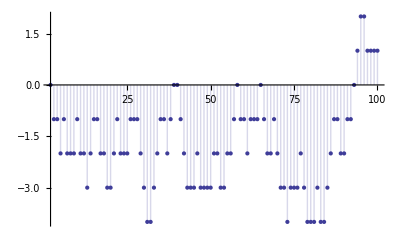

```mathematica
DiscretePlot[ME2b[n,2],{n,2,100}]
```

```mathematica
DiscretePlot[D1f[n,-1,2],{n,2,100}]
```

-Graphics-

```mathematica
DiscretePlot[ME2[n,(3/2)]-(3/2)ME2[n/(3/2),(3/2)],{n,2,100}]
```

-Graphics-

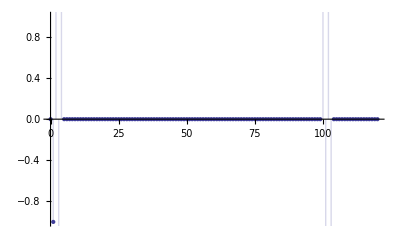

```mathematica
DiscretePlot[(-1)^k (E2a[100,k,1.0001]-1.0001 E2a[100/1.0001,k,1.0001]),{k,0,120},PlotRange->{{0,120},{-1,1}}]
```

```mathematica
D1e[2400,-2,7]
```

E2[2400,0,7] | -2 E2[2400,1,7] | 3 E2[2400,2,7] | -4 E2[2400,3,7] | 5 E2[2400,4,7] | -6 E2[2400,5,7] | 7 E2[2400,6,7] | -8 E2[2400,7,7] | 9 E2[2400,8,7] | -10 E2[2400,9,7] | 11 E2[2400,10,7] | -12 E2[2400,11,7]
14 E2[2400/7,0,7] | -28 E2[2400/7,1,7] | 42 E2[2400/7,2,7] | -56 E2[2400/7,3,7] | 70 E2[2400/7,4,7] | -84 E2[2400/7,5,7] | 98 E2[2400/7,6,7] | -112 E2[2400/7,7,7] | 126 E2[2400/7,8,7] |  |  | 
49 E2[2400/49,0,7] | -98 E2[2400/49,1,7] | 147 E2[2400/49,2,7] | -196 E2[2400/49,3,7] | 245 E2[2400/49,4,7] | -294 E2[2400/49,5,7] |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[1200,-3,2]
```

E2[1200,0,2] | -3 E2[1200,1,2] | 6 E2[1200,2,2] | -10 E2[1200,3,2] | 15 E2[1200,4,2] | -21 E2[1200,5,2] | 28 E2[1200,6,2] | -36 E2[1200,7,2] | 45 E2[1200,8,2] | -55 E2[1200,9,2] | 66 E2[1200,10,2]
6 E2[600,0,2] | -18 E2[600,1,2] | 36 E2[600,2,2] | -60 E2[600,3,2] | 90 E2[600,4,2] | -126 E2[600,5,2] | 168 E2[600,6,2] | -216 E2[600,7,2] | 270 E2[600,8,2] | -330 E2[600,9,2] | 
12 E2[300,0,2] | -36 E2[300,1,2] | 72 E2[300,2,2] | -120 E2[300,3,2] | 180 E2[300,4,2] | -252 E2[300,5,2] | 336 E2[300,6,2] | -432 E2[300,7,2] | 540 E2[300,8,2] |  | 
8 E2[150,0,2] | -24 E2[150,1,2] | 48 E2[150,2,2] | -80 E2[150,3,2] | 120 E2[150,4,2] | -168 E2[150,5,2] | 224 E2[150,6,2] | -288 E2[150,7,2] |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |  |

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[{1.0001^k,(-1)^k (E2a[100,k,1.0001]-1.0001 E2a[100/1.0001,k,1.0001])},{k,0,200}]//TableForm
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$Aborted

```mathematica
N[Table[{k,(-1)^k (E2a[1000,k,ss=2]+ss E2a[1000/ss,k,ss])},{k,0,20}]//TableForm]
```

0. | 3.
1. | 3.
2. | -8.
3. | 25.
4. | -130.
5. | -260.
6. | 22.
7. | -60.
8. | -49.
9. | -8.
10. | 0.
11. | 0.
12. | 0.
13. | 0.
14. | 0.
15. | 0.
16. | 0.
17. | 0.
18. | 0.
19. | 0.
20. | 0.

```mathematica
N[Table[{k,(-1)^k (E2a[10000,k,ss=2]+ss E2a[1000/ss,k,ss])},{k,0,20}]//TableForm]
```

0. | 3.
1. | 3.
2. | 3.
3. | 12.
4. | 297.
5. | -1209.
6. | -796.
7. | 1213.
8. | -182.
9. | 1018.
10. | 939.
11. | 320.
12. | 67.
13. | 1.
14. | 0.
15. | 0.
16. | 0.
17. | 0.
18. | 0.
19. | 0.
20. | 0.

```mathematica
Binomial[z,0]
```

1

```mathematica
Limit[ Sum[ Binomial[z+j-1, z-1]a^j,{j,0,Log[a,n]}]/.z->1,a->1]
```

DirectedInfinity[-1+n]

```mathematica
D1e[100,-3,2]
```

E2[100,0,2] | -3 E2[100,1,2] | 6 E2[100,2,2] | -10 E2[100,3,2] | 15 E2[100,4,2] | -21 E2[100,5,2] | 28 E2[100,6,2]
6 E2[50,0,2] | -18 E2[50,1,2] | 36 E2[50,2,2] | -60 E2[50,3,2] | 90 E2[50,4,2] | -126 E2[50,5,2] | 
12 E2[25,0,2] | -36 E2[25,1,2] | 72 E2[25,2,2] | -120 E2[25,3,2] | 180 E2[25,4,2] |  | 
8 E2[25/2,0,2] | -24 E2[25/2,1,2] | 48 E2[25/2,2,2] | -80 E2[25/2,3,2] |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
$RecursionLimit=1000000
dr[n_,k_,b_]:=DiscretePlot[ Binomial[k+j-1,k-1] b^j (-1)^j
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
```

1000000

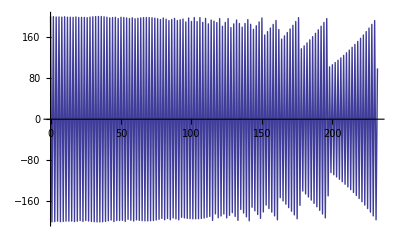

```mathematica
dr[100,1,1.02]
```

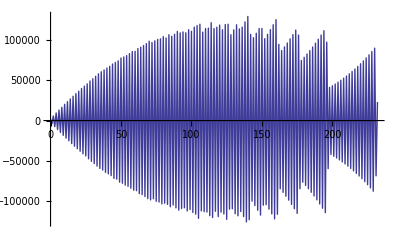

```mathematica
dr[100,2,1.02]
```

```mathematica
Dr2[n_, k_, b_] := DiscretePlot[Sum[ Binomial[k+j-1,k-1] b^j (-1)^j
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,s,s}],{j,0,Log[b,n]}],{s,0,Log[b,n]},PlotRange->{{0,100},{-.1,.1}}]
```

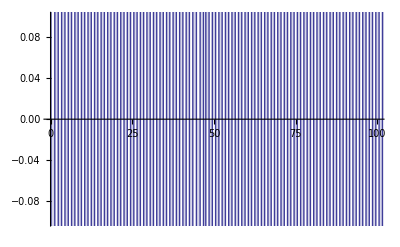

```mathematica
Dr2[5,-1,1.005]
```

```mathematica
Dr3[n_, k_, b_] := Table[{b^s,Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,s,s}],{j,0,Log[b,n]}]},{s,0,Log[b,n]}]//TableForm
```

```mathematica
Dr3[12,-1,1.02]
```

1. | -0.02
1.02 | -0.5756
1.0404 | 2.50217
1.06121 | 0.444801
1.08243 | -2.06826
1.10408 | 5.22111
1.12616 | -16.5302
1.14869 | 24.2717
1.17166 | -34.1435
1.19509 | -52.2886
1.21899 | 172.532
1.24337 | -63.0479
1.26824 | -87.5836
1.29361 | 110.314
1.31948 | 4.31786
1.34587 | -137.993
1.37279 | -31.8071
1.40024 | 229.224
1.42825 | -273.9
1.45681 | 324.691
1.48595 | 1951.99
1.51567 | -6959.36
1.54598 | 7414.56
1.5769 | -2529.08
1.60844 | -113.67
1.64061 | 125.599
1.67342 | -138.353
1.70689 | 104.961
1.74102 | -116.76
1.77584 | 179.896
1.81136 | -196.214
1.84759 | 213.547
1.88454 | -231.939
1.92223 | 251.433
1.96068 | -272.076
1.99989 | -2204.95
2.03989 | 4949.83
2.08069 | -2542.92
2.1223 | -129.849
2.16474 | 139.241
2.20804 | -149.13
2.2522 | 159.536
2.29724 | -170.479
2.34319 | 181.979
2.39005 | -86.7932
2.43785 | 94.8425
2.48661 | -215.515
2.53634 | 229.279
2.58707 | -243.709
2.63881 | 258.832
2.69159 | -274.674
2.74542 | 291.261
2.80033 | -308.621
2.85633 | 326.784
2.91346 | -345.778
2.97173 | -4302.36
3.03117 | 9216.11
3.09179 | -4728.86
3.15362 | -14.5524
3.2167 | 15.0983
3.28103 | -15.6602
3.34665 | 16.2385
3.41358 | -16.8337
3.48186 | 17.4461
3.55149 | -18.0764
3.62252 | 18.7249
3.69497 | -19.3921
3.76887 | 20.0785
3.84425 | -20.7846
3.92114 | 21.5109
3.99956 | 263.311
4.07955 | -272.415
4.16114 | -11.9498
4.24436 | 12.3569
4.32925 | -12.7755
4.41584 | 13.2059
4.50415 | -13.6485
4.59424 | 14.1034
4.68612 | -14.5711
4.77984 | 15.0518
4.87544 | -15.546
4.97295 | 16.0538
5.07241 | -16.5758
5.17386 | 17.1123
5.27733 | -17.6635
5.38288 | 18.23
5.49054 | -18.8121
5.60035 | 19.4101
5.71235 | -20.0246
5.8266 | 20.6559
5.94313 | 524.275
6.062 | -540.704
6.18324 | -0.123665
6.3069 | 0.126138
6.43304 | -0.128661
6.5617 | 0.131234
6.69293 | -0.133859
6.82679 | 0.136536
6.96333 | -0.139267
7.10259 | 0.142052
7.24465 | -0.144893
7.38954 | 0.147791
7.53733 | -0.150747
7.68808 | 0.153762
7.84184 | -0.156837
7.99867 | 0.159973
8.15865 | -0.163173
8.32182 | 0.166436
8.48826 | -0.169765
8.65802 | 0.17316
8.83118 | -0.176624
9.00781 | 0.180156
9.18796 | -0.183759
9.37172 | 0.187434
9.55916 | -0.191183
9.75034 | 0.195007
9.94535 | -0.198907
10.1443 | 0.202885
10.3471 | -0.206943
10.5541 | 0.211082
10.7652 | -0.215303
10.9805 | 0.219609
11.2001 | -0.224002
11.4241 | 0.228482
11.6526 | -0.233051
11.8856 | -11.8856

```mathematica
DD[5,-1]
```

-2

```mathematica
DD[6,-1]
```

-1

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[{k,(-1)^k( E2b[5,k,1.01]-1.01 E2b[5/1.01,k,1.01]),(-1)^(k+1)/k E2b[5,k,1.01] },{k,1,Log[1.01,5]+10}]//TableForm
```

1 | -0.9296 | 8.04
2 | -0.172408 | -8.6204
3 | 0.317254 | 10.5751
4 | -0.506193 | -12.6548
5 | 0.740504 | 14.8101
6 | -1.02149 | -17.0249
7 | 1.35049 | 19.2927
8 | -1.72885 | -21.6106
9 | 2.15796 | 23.9773
10 | -2.63922 | -26.3922
11 | 3.17408 | 28.8553
12 | -3.764 | -31.3667
13 | 4.41048 | 33.9268
14 | -5.11504 | -36.536
15 | 5.87922 | 39.1948
16 | -6.70462 | -41.9039
17 | 7.59284 | 44.6638
18 | -8.54553 | -47.4752
19 | 9.56436 | 50.3387
20 | -10.651 | -53.2552
21 | 11.8073 | 56.2252
22 | 305.027 | -59.2496
23 | -654.173 | 47.2432
24 | 342.316 | -19.4209
25 | 1.28891 | 5.15563
26 | -1.35335 | -5.20519
27 | 1.41895 | 5.25538
28 | -1.48573 | -5.30619
29 | 1.55371 | 5.35761
30 | -1.62289 | -5.40963
31 | 1.6933 | 5.46227
32 | -1.76496 | -5.5155
33 | 1.83788 | 5.56934
34 | -1.91209 | -5.62379
35 | 1.98759 | 5.67883
36 | -2.06442 | -5.73449
37 | 2.14258 | 5.79075
38 | -2.22209 | -5.84762
39 | 2.30299 | 5.9051
40 | -2.38528 | -5.96319
41 | 2.46898 | 6.02191
42 | -2.55412 | -6.08125
43 | 2.64072 | 6.14121
44 | -2.72879 | -6.2018
45 | 2.81836 | 6.26303
46 | -2.90945 | -6.3249
47 | 3.00208 | 6.38741
48 | -3.09627 | -6.45057
49 | 3.19205 | 6.51438
50 | -3.28943 | -6.57885
51 | -82.1737 | 6.64399
52 | 84.6231 | -5.03211
53 | 1.80419 | 3.40413
54 | -1.85629 | -3.43757
55 | 1.90925 | 3.47136
56 | -1.96309 | -3.50551
57 | 2.01781 | 3.54001
58 | -2.07343 | -3.57487
59 | 2.12996 | 3.6101
60 | -2.18741 | -3.64568
61 | 2.2458 | 3.68164
62 | -2.30514 | -3.71797
63 | 2.36544 | 3.75467
64 | -2.42672 | -3.79174
65 | 2.48898 | 3.8292
66 | -2.55225 | -3.86705
67 | 2.61653 | 3.90528
68 | -2.68185 | -3.9439
69 | 2.74821 | 3.98291
70 | -2.81563 | -4.02233
71 | 2.88412 | 4.06214
72 | -2.9537 | -4.10236
73 | 3.02438 | 4.14299
74 | -3.09619 | -4.18404
75 | 3.16912 | 4.2255
76 | -3.24321 | -4.26738
77 | 3.31846 | 4.30968
78 | -3.39489 | -4.35242
79 | 3.47251 | 4.39559
80 | -3.55135 | -4.43919
81 | 3.63142 | 4.48324
82 | -3.71274 | -4.52773
83 | 3.79532 | 4.57267
84 | -3.87918 | -4.61807
85 | 3.96433 | 4.66392
86 | -4.05081 | -4.71024
87 | 4.13861 | 4.75702
88 | -4.22777 | -4.80428
89 | 4.31829 | 4.85201
90 | -4.41021 | -4.90023
91 | 4.50353 | 4.94893
92 | 227.502 | -4.99812
93 | -232.275 | 2.52498
94 | -0.0254806 | -0.027107
95 | 0.0257354 | 0.0270899
96 | -0.0259927 | -0.0270758
97 | 0.0262527 | 0.0270646
98 | -0.0265152 | -0.0270563
99 | 0.0267803 | 0.0270508
100 | -0.0270481 | -0.0270481
101 | 0.0273186 | 0.0270481
102 | -0.0275918 | -0.0270508
103 | 0.0278677 | 0.027056
104 | -0.0281464 | -0.0270638
105 | 0.0284279 | 0.0270742
106 | -0.0287121 | -0.0270869
107 | 0.0289993 | 0.0271021
108 | -0.0292893 | -0.0271197
109 | 0.0295822 | 0.0271396
110 | -0.029878 | -0.0271618
111 | 0.0301768 | 0.0271863
112 | -0.0304785 | -0.027213
113 | 0.0307833 | 0.0272419
114 | -0.0310911 | -0.0272729
115 | 0.031402 | 0.0273061
116 | -0.0317161 | -0.0273414
117 | 0.0320332 | 0.0273788
118 | -0.0323536 | -0.0274183
119 | 0.0326771 | 0.0274597
120 | -0.0330039 | -0.0275032
121 | 0.0333339 | 0.0275487
122 | -0.0336672 | -0.0275961
123 | 0.0340039 | 0.0276455
124 | -0.034344 | -0.0276967
125 | 0.0346874 | 0.0277499
126 | -0.0350343 | -0.027805
127 | 0.0353846 | 0.0278619
128 | -0.0357385 | -0.0279207
129 | 0.0360958 | 0.0279813
130 | -0.0364568 | -0.0280437
131 | 0.0368214 | 0.0281079
132 | -0.0371896 | -0.0281739
133 | 0.0375615 | 0.0282417
134 | -0.0379371 | -0.0283113
135 | 0.0383165 | 0.0283826
136 | -0.0386996 | -0.0284556
137 | 0.0390866 | 0.0285304
138 | -0.0394775 | -0.0286069
139 | 0.0398723 | 0.0286851
140 | -0.040271 | -0.028765
141 | 0.0406737 | 0.0288466
142 | -0.0410804 | -0.0289299
143 | 0.0414912 | 0.0290149
144 | -0.0419062 | -0.0291015
145 | 0.0423252 | 0.0291898
146 | -0.0427485 | -0.0292798
147 | 0.043176 | 0.0293714
148 | -0.0436077 | -0.0294647
149 | 0.0440438 | 0.0295596
150 | -0.0444842 | -0.0296562
151 | 0.0449291 | 0.0297544
152 | -0.0453784 | -0.0298542
153 | 0.0458321 | 0.0299557
154 | -0.0462905 | -0.0300587
155 | 0.0467534 | 0.0301635
156 | -0.0472209 | -0.0302698
157 | 0.0476931 | 0.0303778
158 | -0.04817 | -0.0304874
159 | 0.0486517 | 0.0305986
160 | -0.0491383 | -0.0307114
161 | -4.96296 | 0.0308259
162 | 0. | 0.
163 | 0. | 0.
164 | 0. | 0.
165 | 0. | 0.
166 | 0. | 0.
167 | 0. | 0.
168 | 0. | 0.
169 | 0. | 0.
170 | 0. | 0.
171 | 0. | 0.

```mathematica
-E2b[5,161,1.01]-1.01 E2b[5/1.01,161,1.01]
```

4.96296

```mathematica
(-1)^159( E2b[5,159,1.01]-1.01 E2b[5/1.01,159,1.01])
```

-0.0486517